```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
$Assumptions = s>1
b = 1;
a = 1;

xsol[s_]:= x[s] /. DSolve[{(a*x[s]+b)*x''[s]+a*((x'[s])^2)==a,x[0]==0, x'[0]==0},x[s],s][[1]] //Simplify;

xsol[s]

(*ysol[s_]:=*)
ysol[s_]:= y[s] /.
DSolve[{(a*x[s]+b)*y''[s]+a*((x'[s])*(y'[s]))==0,y[0]==0,y'[0]==3},y[s],s][[1]] /.{x[0]->0, Ax->1}

ysol1[s]=ysol[s] /.{x[s_]->xsol[s]}
(*ysol1[s] /. {x[s_]-> xsol[s]}*)
```

s>1

-1+√(1+s^2)

3 ArcSinh[1]+3 (-ArcSinh[1]+ArcSinh[s])

-1+√(1+4 s+s^2)

```mathematica
Manipulate[{xsol[s],ysol1[s]}/.{s-> s0},{s0,0,10}]
```

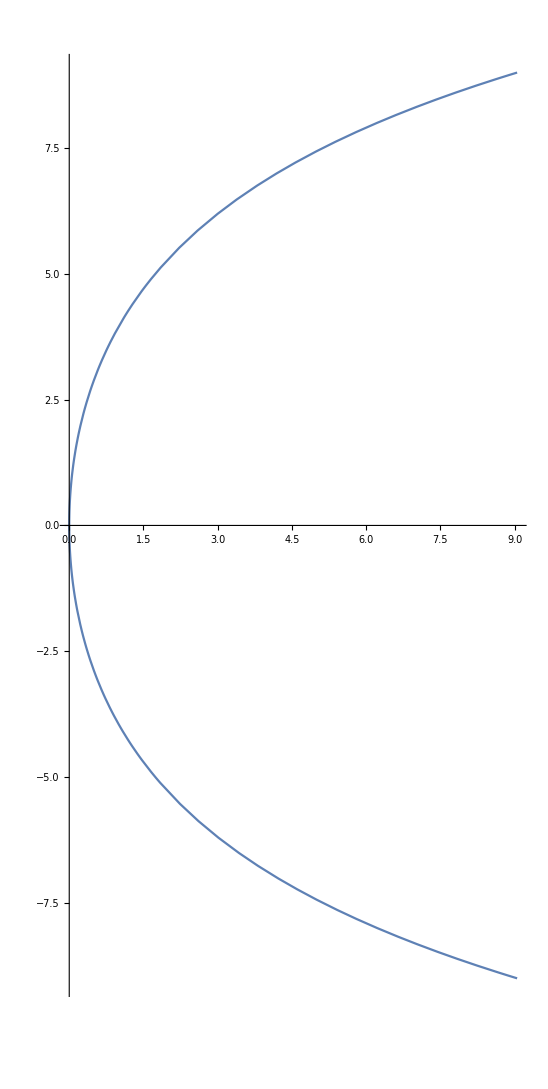

```mathematica
ParametricPlot[{xsol[s],ysol1[s]}/.{s-> s0},{s0,-10,10}]
```

```mathematica
Show[ParametricPlot[{xsol[s],ysol1[s]}/.{s-> s0},{s0,-10,10}],Graphics[Point[{xsol[sp],ysol1[sp]}/.{sp-> 0}]]]
```

-Graphics-